```mathematica
(*Author: HKUST,Robotics Institute, William Wu, Wenchao DING*)
Manipulate[
r1 = d/2-δ+df;
r2 = d/2 +δ+df;
c0=Circle[{0,0},r1];
c1 = Circle[{d,0},r2];
rc0 = Circle[{0,0},r1+dr];
rc1 = Circle[{d,0},r2+dr];
θ = ArcSin[(r2-r1)/d];
p0 = {-r1 Sin[θ],r1 Cos[θ]};
p1 = {d-r2 Sin[θ],r2 Cos[θ]};
p2 = {-r1 Sin[θ],-r1 Cos[θ]};
p3 = {d-r2 Sin[θ],-r2 Cos[θ]};
ans = Solve[{x,y}∈c1&&{x,y}∈c0,{x,y}];
ans2 = Solve[{x,y}∈rc1&&{x,y}∈rc0,{x,y}];{
Solve[{x,y}∈rc1&&{x,y}∈rc0&&({x,y}∈InfiniteLine[{p0,p1}]||{x,y}∈InfiniteLine[{p2,p3}]),dr],
Graphics[{{Green,InfiniteLine[{p0,p1}],InfiniteLine[{p2,p3}]},{Blue,c0,c1,rc0,rc1},{Red,PointSize[0.01],Point[{x,y}]/.ans,Point[{x,y}]/.ans2}}]/.{d->cd,δ->cδ,df->cdf,dr->cdr},{Red,rc0,rc1}},
{cd,1,10},{cδ,0,cd/2},{cdf,0.01,10},{cdr,0.01,3}
]
```

```mathematica
r1 = d/2-δ+df;
r2 = d/2 +δ+df;
c0=Circle[{0,0},r1];
c1 = Circle[{d,0},r2];
rc0 = Circle[{0,0},r1+dr];
rc1 = Circle[{d,0},r2+dr];
θ = ArcSin[(r2-r1)/d];
p0 = {-r1 Sin[θ],r1 Cos[θ]}
p1 = {d-r2 Sin[θ],r2 Cos[θ]}
p2 = {-r1 Sin[θ],-r1 Cos[θ]}
p3 = {d-r2 Sin[θ],-r2 Cos[θ]}
ans = Solve[d>0&&δ>0&&df>0&&{x,y}∈c1&&{x,y}∈c0,{x,y}]
ans2 = Solve[d>0&&δ>0&&df>0&&{x,y}∈rc1&&{x,y}∈rc0,{x,y}]
Solve[d>0&&δ>0&&df>0&&{x,y}∈rc1&&{x,y}∈rc0&&({x,y}∈InfiniteLine[{p0,p1}]||{x,y}∈InfiniteLine[{p2,p3}]),{x,y,dr}]
```

{(2 δ (-d/2-df+δ))/d,(d/2+df-δ) √(1-(4 δ^2)/d^2)}

{d-(2 δ (d/2+df+δ))/d,(d/2+df+δ) √(1-(4 δ^2)/d^2)}

{(2 δ (-d/2-df+δ))/d,(-d/2-df+δ) √(1-(4 δ^2)/d^2)}

{d-(2 δ (d/2+df+δ))/d,(-d/2-df-δ) √(1-(4 δ^2)/d^2)}

{{x→ConditionalExpression[(d^2-2 d δ-4 df δ)/(2 d),d>2 δ&&df>0&&δ>0],y→ConditionalExpression[-1/2 √(-3 d^2+4 d df+4 df^2+4 d δ+8 df δ+4 δ^2+4 (d^2-2 d δ-4 df δ)-((d^2-2 d δ-4 df δ)^2)/d^2),d>2 δ&&df>0&&δ>0]},{x→ConditionalExpression[(d^2-2 d δ-4 df δ)/(2 d),d>2 δ&&df>0&&δ>0],y→ConditionalExpression[1/2 √(-3 d^2+4 d df+4 df^2+4 d δ+8 df δ+4 δ^2+4 (d^2-2 d δ-4 df δ)-((d^2-2 d δ-4 df δ)^2)/d^2),d>2 δ&&df>0&&δ>0]}}

{{x→ConditionalExpression[(d^2-2 d δ-4 df δ-4 dr δ)/(2 d),d>2 δ&&df>0&&dr>-df&&δ>0],y→ConditionalExpression[-1/2 √(-3 d^2+4 d df+4 df^2+4 d dr+8 df dr+4 dr^2+4 d δ+8 df δ+8 dr δ+4 δ^2+4 (d^2-2 d δ-4 df δ-4 dr δ)-((d^2-2 d δ-4 df δ-4 dr δ)^2)/d^2),d>2 δ&&df>0&&dr>-df&&δ>0]},{x→ConditionalExpression[(d^2-2 d δ-4 df δ-4 dr δ)/(2 d),d>2 δ&&df>0&&dr>-df&&δ>0],y→ConditionalExpression[1/2 √(-3 d^2+4 d df+4 df^2+4 d dr+8 df dr+4 dr^2+4 d δ+8 df δ+8 dr δ+4 δ^2+4 (d^2-2 d δ-4 df δ-4 dr δ)-((d^2-2 d δ-4 df δ-4 dr δ)^2)/d^2),d>2 δ&&df>0&&dr>-df&&δ>0]}}

{{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],y→ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)]},{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],y→ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)]},{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y→ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]},{x→ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y→ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr→ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]}}

```mathematica
{{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],y->ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)]},{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],y->ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)]},{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y->ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]},{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y->ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]}}
```

```mathematica
Plot3D[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2))/.d->2,{δ,0,1},{df,δ,1},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2))/.d->2,{δ,0,1},{df,δ,1},PlotRange->All]
```

-Graphics3D-

```mathematica
pdr = dr/.{{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],y->ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)]},{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],y->ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))-√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),(d>2 √2 √(δ^2)&&df>0&&δ>0)||(2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0)]},{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y->ConditionalExpression[-1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]},{x->ConditionalExpression[(d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],y->ConditionalExpression[1/4 √(1/δ^2(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0],dr->ConditionalExpression[1/2 (-d-2 df+2 δ)+√(((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2+1/(16 δ^2)(d^4-8 d^2 δ^2+16 δ^4-4 d^3 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+16 d δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))+4 d^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2-16 δ^2 ((d^4-8 d^2 δ^2+8 d δ^3+16 df δ^3)/(2 d (d^2-8 δ^2))+√2 √((d^6 δ^2+2 d^5 df δ^2+2 d^4 df^2 δ^2-12 d^4 δ^4-16 d^3 df δ^4-16 d^2 df^2 δ^4+48 d^2 δ^6+32 d df δ^6+32 df^2 δ^6-64 δ^8)/(d^2 (d^2-8 δ^2)^2)))^2)),2 δ<d<2 √2 √(δ^2)&&df>0&&δ>0]}};
Plot3D[#,{δ,0,1},{df,δ,1},PlotRange->{0,2}]&/@(pdr/.d->2)
Plot[#,{δ,0,1}]&/@(pdr/.{d->2,df->0.5})
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
|
```

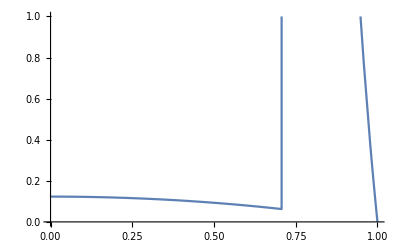
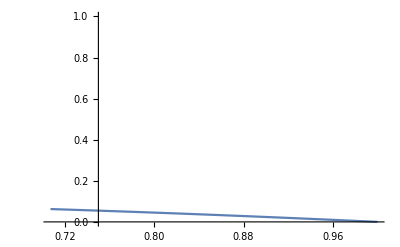
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[#,{δ,0,1},PlotRange->{0,1}]&/@(pdr/.{d->2,df->3})
```

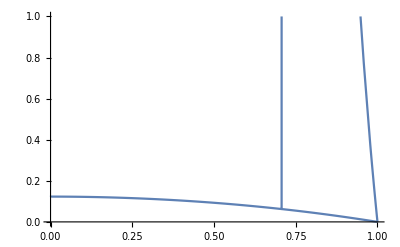

```mathematica
Show[{%[[1]],%[[3]]}]
```

```mathematica
Maximize[{#,δ<df,δ<0.7}/.d->2,{δ,df}]&/@Take[pdr,2]
```

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {-df + δ ≤ 0, 1 - √2\ √δ^2 ≤ 0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

{{0.414251,{δ→7.33021×10^-7,df→3.12877×10^-7}},{0.414251,{δ→7.33021×10^-7,df→3.12877×10^-7}}}

```mathematica
N[Sqrt[2]]
```

1.41421